#### Sezione d.

```mathematica
ClearAll["Global`*"]
```

```mathematica
f[μ_,x_]:= μ x (1-x)
fn[μ_,x_,n_]:= Nest[f[μ,#]&,x,n]
fnList[μ_,x_,n_]:= NestList[f[μ,#]&,x,n]
fnC=Compile[{{μ,_Real},{x,_Real},{n,_Integer}},Nest[μ #(1-#)&,x,n]];
```

```mathematica
With[{test=First/@{fn[3.5,0.4,10^7];//Timing,fnC[3.5,0.4,10^7];//Timing}},(First[test]-Last[test])/First[test]]
```

è tremendamente più efficiente usare la funzione compilata se il numero di iterazioni iniziale è alto; si risparmia il 98% del tempo.

```mathematica
(*Manipulate[ListPlot[fn[μ,0.4,#]&/@Range[100]],{μ,0,4}]*)
```

sappiamo che incontrare orbite periodiche (di periodo k) vuol dire che (asintoticamente) le orbite ciclano tra k valori distinti.
data la convergenza “veloce” al valore finale costruisco una funzione “conf” che dato un μ itera f un certo numero abbastanza alto di volte (iterations) e controlla la differenza tra le successive k=2^n

questo processo produrrà il numero corretto di orbite (modulo “piccolissime” differenze, motivo per cui moltiplico per 10^4ed arrotondo)
il numero restituito da “conf” è il numero di valori diversi tra cui ciclano le orbite.

```mathematica
conf[μ_,n_,iterations_]:=Length[Union[Round[10^4(fnC[μ,0.4,iterations+#]-fnC[μ,0.4,iterations]),1]& /@Range[2^n]]]
```

il 10^4è arbitrario e non andrà bene per la ricerca di un μ_n abbastanza elevato. possiamo automatizzare anche quello

```mathematica
scale[μ_,iterations_,n_]:=1/2((1/RealAbs[fn[μ,0.4,Position[Max[fnC[μ,0.4,iterations+#]&/@Range[2^n]]]]-fnC[μ,0.4,Position[Max[fn[μ,0.4,iterations+#]&/@Range[2^n]]]+1]])+(1/RealAbs[fnC[μ,0.4,iterations]-fnC[μ,0.4,iterations+2^n]]))
```

```mathematica
conf2[μ_,n_,iterations_]:=Length[Union[Round[Scale[μ,iterations,n](fnC[μ,0.4,iterations+#]-fnC[μ,0.4,iterations]),1]& /@Range[2^n]]]
```

```mathematica
(*data=ParallelTable[{μ,conf[μ,7,10000]},{μ,2.8,3.5,10^-6}];*)
```

per ottimizzare i tempi si può utilizzare un numero di iterazioni iniziale più basso (come per il numero di iterazioni utilizzate per cercare il punto) per trovare i primi punti e alzarlo man mano
questo processo si potrebbe automatizzare conoscendo più o meno dove sono i punti e regolando automaticamente il range di conseguenza

#### Troviamo i punti a manina:

```mathematica
databyhand=Flatten[ParallelTable[{μ,conf[μ,#⟦1⟧,#⟦2⟧]},{μ,#⟦3⟧,#⟦4⟧,10^(-#⟦5⟧)}]&/@{{4,300,2.95,3.05,5},{4,600,3.35,3.5,5},{5,1000,3.5,3.57,6},{6,5000,3.564,3.57,6},{7,10000,3.568,3.57,6}},1];
```

```mathematica
databyhand//Short
```

```mathematica
Export[NotebookDirectory[]<>"databyhand.csv",%]
```

```mathematica
Import[NotebookDirectory[]<>"databyhand.csv"]
```

```mathematica
(*databyhand = Import["githubblabla così da non doversela ricalcolare ogni cazzo di volta"]*)
(*Sono molto d'accordo: lo faccio subito*)
```

```mathematica
databyhand=Import["https://raw.githubusercontent.com/ZinRicky/cammelli-tonanti/master/01_Esame/03_Dati/D_databyhand.csv"];
```

```mathematica
ListPlot[databyhand,PlotRange->{All,{0,20}},AspectRatio->1/3,Ticks->{Range[2.5,4,0.05],Range[0,30,2]},ImageSize->Full]
```

#### con relativo check:

```mathematica
data0= ParallelTable[{μ,conf[μ,2,200]},{μ,2.9,3.1,10^-6}];
```

```mathematica
ListPlot[data0]
```

```mathematica
First@Last@Cases[data0,{_,1}]
```

```mathematica
data1=ParallelTable[{μ,conf[μ,4,500]},{μ,3.1,3.5,10^-4}];
```

```mathematica
ListPlot[data1]
```

```mathematica
First@Last@Cases[data1,{_,2}]
```

```mathematica
data2=ParallelTable[{μ,conf[μ,5,1000]},{μ,3.5,3.57,10^-5}];
```

```mathematica
ListPlot[data2]
```

```mathematica
First@Last@Cases[data2,{_,4}]
```

```mathematica
First@Last@Cases[data2,{_,8}]
```

```mathematica
data3=ParallelTable[{μ,conf[μ,6,5000]},{μ,3.564,3.57,10^-5}];
```

```mathematica
ListPlot[data3]
```

```mathematica
First@Last@Cases[data3,{_,16}]
```

```mathematica
First@Last@Cases[data3,{_,32}]
```

```mathematica
data4=ParallelTable[{μ,conf[μ,7,10000]},{μ,3.565,3.5702,10^-6}];
```

```mathematica
ListPlot[data4]
```

```mathematica
First@Last@Cases[data4,{_,64}]
```

μ_∞≈3.57

```mathematica
data=Flatten[{data0,data1,data2,data3,data4},1];
```

#### aumentiamo la precisione

```mathematica
dist[μ_,x0_,Ν_,n_]:=Abs[fnC[μ,x0,Ν]-fnC[μ,x0,Ν+2^n]]
indagine[n_,x0_,Ν_,{min_,max_,step_}]:=ParallelTable[{μ,dist[μ,x0,Ν,n]},{μ,min,max,step}]
indaginePlot[n_,x0_,Ν_,{min_,max_,step_}]:=ListPlot[indagine[n,x0,Ν,{min,max,step}],AspectRatio->1,PlotRange->Full]
sospetto[n_,x0_,Ν_,{min_,max_,step_}]:=Module[
{
ind=indagine[n,x0,Ν,{min,max,step}],
val,
spike
},
val=Last/@ind;
spike=Max@val;
Cases[ind,{_,spike}]
]
colpevole[n_,x0_,Ν_,{min_,max_,step_}]:=sospetto[n,x0,Ν,{min,max,step}]⟦1,1⟧
```

```mathematica
ricerca[n_,step_]:={First@Last@Cases[databyhand,{_,2^n}]-10^3 step,First@Last@Cases[databyhand,{_,2^n}]+10^3 step,step}
```

```mathematica
ricerca[#,10^-Max[{5,#+2}]]&/@Range[0,5]
```

```mathematica
colpevole[1,0.4,10^5,ricerca[0,10^-Max[{5,2}]]]
```

2.96593

ci mette davvero tanto tempo e non ho idea di come ottimizzarlo

```mathematica
colpevole[6,0.4,10^5,ricerca[4,10^-8]]
```

3.56876

#### da concludere

```mathematica
μ[n_]:= colpevole[n+2,0.4,10^5,ricerca[n,10^-Max[{5,n+2}]]]
```

```mathematica
NumberForm[μ[1],20]
```

```mathematica
(μ[1]-(1+√6))/(1+√6)//Abs
```

```mathematica
μs=μ[#]&/@Range[0,6]
```

```mathematica
feigenbaum =Table[(μs⟦n⟧-μs⟦n-1⟧)/(μs⟦n+1⟧-μs⟦n⟧),{n,2,6}]
```

c’è ancora qualcosina da aggiustare ma siamo sulla strada giusta, i tempi son decenti e la ricerca funziona

```mathematica
GeometricMean[Drop[feigenbaum,{5}]]
```

ha senso farlo?
probabilmente nO! (ma sticazzi)
la costante è circa quella, con dati più precisi si potrebbe far meglio ma dovrei lavorarci sopra e sono pigro.

#### cerchiamo μ_∞

```mathematica
ListPlot[Differences[μ[#]&/@Range[0,6]]]
```

```mathematica
NonlinearModelFit[μ[#]&/@Range[0,6],,{},x]
```

```mathematica
Plot[0.4019466597722899^x,{x,0,4}]
```

```mathematica
μ[#]&/@Range[0,6]
```

senza fare fit è ovvio che il limite è attorno a 3.57
avremo un’ulteriore conferma nella parte E;

“Alla biforcazione n, ogni punto fisso di f^(2^n) biforca producendo due punti fissi di f^(2^(n+1)); al crescere di μ, la distanza fra questi due punti fissi aumenta. Sia d(n+1) la loro distanza quando essi biforcano. Si riesce a stabilire l’asintotica di d(n+1)/d(n) ?”

questo assume che quando i punti biforcano la distanza tra loro sia uguale, ossia che (ad esempio) quando le orbite di periodo 2 biforcano in orbite di periodo 4, la distanza tra i punti nelle due forche sia uguale;
vediamo un po’

```mathematica
Manipulate[fn[μ[0],0.4,n],{n,0,100,1}]
```

```mathematica
d[n_]:=Min[Abs[fn[μ[n],0.4,1000]-fn[μ[n],0.4,1000+#]&/@Range[2^n]]]
```

```mathematica
ListPlot[d[#]&/@Range[5]]
```

≈0.42

si può migliorare il tutto? yup.

#### Cerchiamo l’orbita di periodo 3 (per la sezione F)

```mathematica
dataμp3=ParallelTable[{μ,conf[μ,2,3000]},{μ,3.82,3.85,10^-6}];
```

```mathematica
ListPlot[dataμp3]
```

#### Universalità

```mathematica
s[λ_,x_]:= λ Sin[π x]
sn=Compile[{{λ,_Real},{x,_Real},{n,_Integer}},Nest[s[λ,π #]&,x,n]]
```

CompiledFunction[…]

```mathematica
attrattivoPlot2[nx_,n_,{μ0_,μ1_,η_}]:=With[{f=Function[{μ,x},μ Sin[π x]]},
ListPlot[
Union@Flatten[Table[
ParallelTable[
{μ,FixedPoint[Chop[f[μ,#]]&,x0,n]},{μ,Subdivide[μ0,μ1,η]}],
{x0,Subdivide[0,1.,nx]}
],1],
PlotStyle->{AbsolutePointSize[0.015],Black},
PlotRange->{{μ0,μ1},{0,1}},AspectRatio->Automatic,
Ticks->{Subdivide[0,4.,20],Subdivide[0,1.,10]}
]
]
```

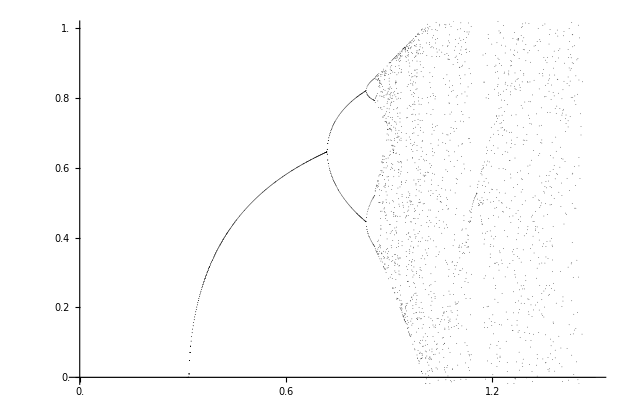

```mathematica
attrattivoPlot2[15,10^3,{0,1.5,10^3}]
```

```mathematica
Manipulate[ListPlot[sn[λ,0.4,#]&/@Range[100]],{λ,0,4}]
```

```mathematica
cons[λ_,n_,iterations_]:=Length[Union[Round[10^4(sn[λ,0.4,iterations+#]-sn[λ,0.4,iterations]),1]& /@Range[2^n]]]
```

```mathematica
data20=ParallelTable[{λ,cons[λ,4,1000]},{λ,0.,4.,10^-2}];
```

```mathematica
ListPlot[data20]
```

```mathematica
data21=ParallelTable[{λ,cons[λ,0.4,500]},{λ,2.,2.5,10^-5}];
```